# Absorption Imaging in High Magnetic Field for Na23 at D2 line

Here we show the zeeman spliting for D2 line(Ground state and Excited state) of Na23, then calculate the dipole matrix of it under high magnetic field. By analyze dipole matrix, we give the possible way for HF-imaging of different spin states of Na23.

Load the package. Here we use the AtomicDensityMatrix tool for getting atomic information(such as Rb87 and Na23)

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<AtomicDensityMatrix`
```

```mathematica
<<Units`
```

Set options for DensityMatrix and a plotting function.

```mathematica
SetOptions[DensityMatrix,TimeDependence->False,ComplexExpandVariables->Subscript];
```

```mathematica
SetOptions[ListLinePlot,PlotRange->All,ImageSize->Medium,Frame->True];
```

Choose a transition. AtomicTransition just returns the names of the states associated with the given transition, which we can use to find the associated data in the AtomicData database.

```mathematica
{gstate,estate}=AtomicTransition["Na23","D2"]
```

{{Na,23,{Ne,{3,s}},{2,S,1/2}},{Na,23,{Ne,{3,p}},{2,P,3/2}}}

Get the list of quantum numbers and other information that we will use to set up the atomic system. We could also include the additional numerical atomic parameters in this list, but it can be more convenient to substitute their values in later.

```mathematica
{gQuantumNumbers,eQuantumNumbers}={AtomicData[gstate,{J,L,S,NuclearSpin,NaturalWidth,Energy}],
AtomicData[estate,{J,L,S,NuclearSpin}]}
```

{{J→1/2,L→0,S→1/2,NuclearSpin→3/2,NaturalWidth→0,Energy→0},{J→3/2,L→1,S→1/2,NuclearSpin→3/2}}

Create the list of sublevels in the atomic system. We specify BranchingRatio[1]→1, which means that the upper J' state decays with 100% probability to the lower J state. The individual F'→F branching ratios are calculated automatically. g-factors are also calculated automatically from the specified values for F, J, L, S, and NuclearSpin.

```mathematica
system=Sublevels@{
AtomicState[1,gQuantumNumbers],AtomicState[2,Append[eQuantumNumbers,BranchingRatio[1]->1]]
};
```

Following diagram shows all states involved in this calculation.

```mathematica
Style[TableForm[system],Small]
```

AtomicState[1,J→1/2,L→0,S→1/2,NuclearSpin→3/2,NaturalWidth→0,Energy→0,F→2,M→2]
AtomicState[1,J→1/2,L→0,S→1/2,NuclearSpin→3/2,NaturalWidth→0,Energy→0,F→2,M→1]
AtomicState[1,J→1/2,L→0,S→1/2,NuclearSpin→3/2,NaturalWidth→0,Energy→0,F→2,M→0]
AtomicState[1,J→1/2,L→0,S→1/2,NuclearSpin→3/2,NaturalWidth→0,Energy→0,F→2,M→-1]
AtomicState[1,J→1/2,L→0,S→1/2,NuclearSpin→3/2,NaturalWidth→0,Energy→0,F→2,M→-2]
AtomicState[1,J→1/2,L→0,S→1/2,NuclearSpin→3/2,NaturalWidth→0,Energy→0,F→1,M→1]
AtomicState[1,J→1/2,L→0,S→1/2,NuclearSpin→3/2,NaturalWidth→0,Energy→0,F→1,M→0]
AtomicState[1,J→1/2,L→0,S→1/2,NuclearSpin→3/2,NaturalWidth→0,Energy→0,F→1,M→-1]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→3,M→3]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→3,M→2]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→3,M→1]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→3,M→0]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→3,M→-1]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→3,M→-2]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→3,M→-3]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→2,M→2]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→2,M→1]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→2,M→0]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→2,M→-1]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→2,M→-2]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→1,M→1]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→1,M→0]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→1,M→-1]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→0,M→0]

Here are the numerical parameters for the atomic system that we will substitute in later.

```mathematica
atomicData=Join[
AtomicData[gstate,StateLabel->1],
AtomicData[estate,StateLabel->2],{c->SpeedOfLight,ℏ->PlanckConstantReduced,ϵ0->VacuumPermittivity}
]
```

{ElementName[1]→Sodium,ElementSymbol[1]→Na,AtomicNumber[1]→11,AtomicWeight[1]→23,Abundance[1]→1,NuclearSpin[1]→3/2,J[1]→1/2,L[1]→0,S[1]→1/2,NaturalWidth[1]→0,Energy[1]→0,HyperfineA[1]→(5565.73 Mega)/Second,HyperfineB[1]→0,Parity[1]→Even,Wavenumber[1]→0,Lifetime[1]→Second ∞,ElementName[2]→Sodium,ElementSymbol[2]→Na,AtomicNumber[2]→11,AtomicWeight[2]→23,Abundance[2]→1,NuclearSpin[2]→3/2,J[2]→3/2,L[2]→1,S[2]→1/2,NaturalWidth[2]→(61.5415 Mega)/Second,Energy[2]→(3.19719×10^9 Mega)/Second,HyperfineA[2]→(116.453 Mega)/Second,HyperfineB[2]→(17.1154 Mega)/Second,Parity[2]→Odd,Wavenumber[2]→16973.4/Centimeter,Lifetime[2]→16.2492 Nano Second,c→(299792458 Meter)/Second,ℏ→1.05457×10^-34 Joule Second,ϵ0→(625000 Ampere Second)/(22468879468420441 Meter π Volt)}

Now we form the Hamiltonian and compute its eigenenergy and eigenstates(Unitary transformation from |F,mF> to new eigenstates)

Form the Hamiltonian assuming  a z-directed magnetic field with nominal Larmor frequency Ω_L.

```mathematica
Style[MatrixForm[h=Hamiltonian[system,MagneticField->{0,0,ΩL/BohrMagneton}]],Small]
```

(ΩL+(3 HyperfineA[1])/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ΩL/2+(3 HyperfineA[1])/4 | 0 | 0 | 0 | (√3 ΩL)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (3 HyperfineA[1])/4 | 0 | 0 | 0 | ΩL | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ΩL/2+(3 HyperfineA[1])/4 | 0 | 0 | 0 | (√3 ΩL)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ΩL+(3 HyperfineA[1])/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (√3 ΩL)/2 | 0 | 0 | 0 | -ΩL/2-(5 HyperfineA[1])/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ΩL | 0 | 0 | 0 | -(5 HyperfineA[1])/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (√3 ΩL)/2 | 0 | 0 | 0 | ΩL/2-(5 HyperfineA[1])/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ΩL+Energy[2]+(9 HyperfineA[2])/4+HyperfineB[2]/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (4 ΩL)/3+Energy[2]+(9 HyperfineA[2])/4+HyperfineB[2]/4 | 0 | 0 | 0 | 0 | 0 | (2 ΩL)/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 ΩL)/3+Energy[2]+(9 HyperfineA[2])/4+HyperfineB[2]/4 | 0 | 0 | 0 | 0 | 0 | 4/3 √(2/5) ΩL | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Energy[2]+(9 HyperfineA[2])/4+HyperfineB[2]/4 | 0 | 0 | 0 | 0 | 0 | (2 ΩL)/(√5) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 ΩL)/3+Energy[2]+(9 HyperfineA[2])/4+HyperfineB[2]/4 | 0 | 0 | 0 | 0 | 0 | 4/3 √(2/5) ΩL | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(4 ΩL)/3+Energy[2]+(9 HyperfineA[2])/4+HyperfineB[2]/4 | 0 | 0 | 0 | 0 | 0 | (2 ΩL)/3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ΩL+Energy[2]+(9 HyperfineA[2])/4+HyperfineB[2]/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 ΩL)/3 | 0 | 0 | 0 | 0 | 0 | (4 ΩL)/3+Energy[2]-(3 HyperfineA[2])/4-(3 HyperfineB[2])/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/3 √(2/5) ΩL | 0 | 0 | 0 | 0 | 0 | (2 ΩL)/3+Energy[2]-(3 HyperfineA[2])/4-(3 HyperfineB[2])/4 | 0 | 0 | 0 | (4 ΩL)/(√15) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 ΩL)/(√5) | 0 | 0 | 0 | 0 | 0 | Energy[2]-(3 HyperfineA[2])/4-(3 HyperfineB[2])/4 | 0 | 0 | 0 | (8 ΩL)/(3 √5) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/3 √(2/5) ΩL | 0 | 0 | 0 | 0 | 0 | -(2 ΩL)/3+Energy[2]-(3 HyperfineA[2])/4-(3 HyperfineB[2])/4 | 0 | 0 | 0 | (4 ΩL)/(√15) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 ΩL)/3 | 0 | 0 | 0 | 0 | 0 | -(4 ΩL)/3+Energy[2]-(3 HyperfineA[2])/4-(3 HyperfineB[2])/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (4 ΩL)/(√15) | 0 | 0 | 0 | (2 ΩL)/3+Energy[2]-(11 HyperfineA[2])/4+HyperfineB[2]/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (8 ΩL)/(3 √5) | 0 | 0 | 0 | Energy[2]-(11 HyperfineA[2])/4+HyperfineB[2]/4 | 0 | (2 √5 ΩL)/3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (4 ΩL)/(√15) | 0 | 0 | 0 | -(2 ΩL)/3+Energy[2]-(11 HyperfineA[2])/4+HyperfineB[2]/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 √5 ΩL)/3 | 0 | Energy[2]-(15 HyperfineA[2])/4+(5 HyperfineB[2])/4)

Draw the level diagram for the truncated system, showing the optical and magnetic-field interactions.

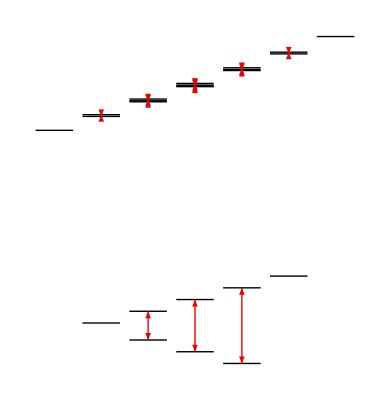

```mathematica
LevelDiagram[system,h/.Energy[2]->5/.atomicData/.{Mega-> 10^-4,Second->1,ΩL->0.5}]
```

Now we write the various input parameters in terms of experimentally relevant quantities.

ExpandDipoleRME expresses the reduced dipole matrix element in terms of the natural width and energy of the transition.

```mathematica
dADM=ExpandDipoleRME[system,ReducedME[1,{Dipole,1},2]]
```

√3 √(NaturalWidth[2]/Energy[2]^3)

Convert ADM units to cgs by multiplying by √(ℏ c^3), and then to SI by multiplying by √(4 π ϵ_0).

```mathematica
dSI=Convert[dADM √(ℏ c^3)√(4 π ϵ0)/.atomicData,Coulomb Meter]
```

4.2261×10^-29 Coulomb Meter

Write the optical electric field (in V/m)  in terms of the light intensity (in mW/cm^2).

```mathematica
E0=Convert[√(2Int(Milli Watt/Centimeter^2)/(c ϵ0))/.atomicData//N,Volt/Meter]
```

(86.8021 √Int Volt)/Meter

Write the Rabi frequency in terms of the light intensity.

```mathematica
ΩR/.rabi/.Int->0.16
```

(1.39141×10^7)/Second

```mathematica
rabi=ΩR->Convert[E0 dSI/ℏ/.atomicData,1/Second]
```

ΩR→(3.47852×10^7 √Int)/Second

Write the Larmor frequency in terms of the magnetic field in Gauss.

```mathematica
larmor=ΩL->Convert[b Gauss BohrMagneton/ℏ/.atomicData,1/Second]
```

ΩL→(8.79411×10^6 b)/Second

```mathematica
MatrixForm/@({energies,states}=Chop[Eigensystem[h/.larmor/.atomicData/.Mega->10^6/.Second->1/.b->0.1],10^-7])
```

{(3.19719×10^15
3.19719×10^15
3.19719×10^15
3.19719×10^15
3.19719×10^15
3.19719×10^15
3.19719×10^15
3.19719×10^15
3.19719×10^15
3.19719×10^15
3.19719×10^15
3.19719×10^15
3.19719×10^15
3.19719×10^15
3.19719×10^15
3.19719×10^15
-6.9576×10^9
-6.95716×10^9
-6.95672×10^9
4.17518×10^9
4.17474×10^9
4.1743×10^9
4.17386×10^9
4.17342×10^9),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.999999 | 0 | 0 | 0 | 0 | 0 | 0.00159977 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.999998 | 0 | 0 | 0 | 0 | 0 | -0.00202357 | 0 | 0 | 0 | -3.15648×10^-6 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.999998 | 0 | 0 | 0 | 0 | 0 | -0.00214632 | 0 | 0 | 0 | -3.8659×10^-6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.999998 | 0 | 0 | 0 | 0 | 0 | -0.00202357 | 0 | 0 | 0 | -3.15648×10^-6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.999999 | 0 | 0 | 0 | 0 | 0 | 0.00159977 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00159977 | 0 | 0 | 0 | 0 | 0 | -0.999999 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00202356 | 0 | 0 | 0 | 0 | 0 | 0.999989 | 0 | 0 | 0 | 0.00420887 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00214631 | 0 | 0 | 0 | 0 | 0 | 0.999986 | 0 | 0 | 0 | 0.00486007 | 0 | 0.000020218
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00202356 | 0 | 0 | 0 | 0 | 0 | 0.999989 | 0 | 0 | 0 | 0.00420887 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00159977 | 0 | 0 | 0 | 0 | 0 | 0.999999 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.36049×10^-6 | 0 | 0 | 0 | 0 | 0 | 0.00420887 | 0 | 0 | 0 | -0.999991 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6.56531×10^-6 | 0 | 0 | 0 | 0 | 0 | 0.00485991 | 0 | 0 | 0 | -0.999901 | 0 | -0.013194
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.36048×10^-6 | 0 | 0 | 0 | 0 | 0 | 0.00420887 | 0 | 0 | 0 | -0.999991 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000439079 | 0 | 0 | 0 | -0.013194 | 0 | 0.999913
0 | -0.0000684126 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.0000790023 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.0000684234 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1. | 0 | 0 | 0 | -0.0000684126 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0.0000790023 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1. | 0 | 0 | 0 | -0.0000684234 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

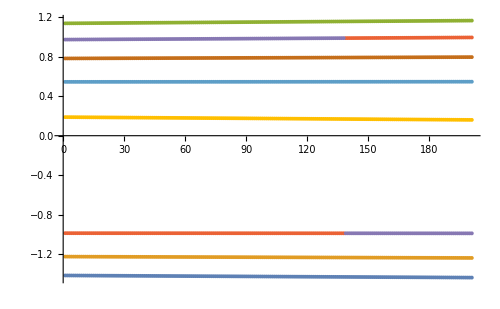

```mathematica
ListPlot[groundZeeman=1/(2π)10^-9*Transpose@Table[Eigenvalues[h/.larmor/.atomicData/.Mega->10^6/.Second->1][[-8;;-1]],{b,340,360,0.1}]]
```

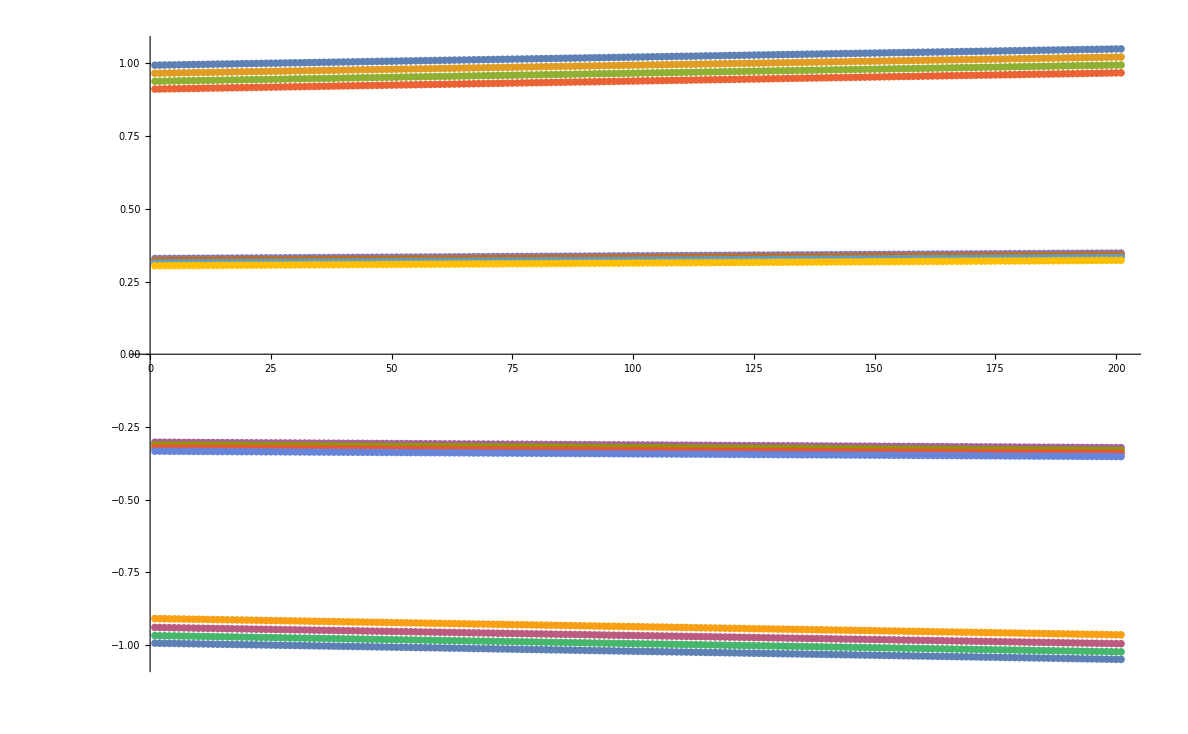

```mathematica
ListPlot[excitedZeeman=-(1/(2π)10^-9 Energy[2]/.atomicData/.Mega->10^6/.Second->1)+1/(2π)10^-9 Transpose@Table[Eigenvalues[h/.larmor/.atomicData/.Mega->10^6/.Second->1][[1;;16]],{b,340,360,0.1}]]
```

```mathematica
chart=Table[{(x-1)*0.1+340,(1771.626-(-1000*(excitedZeeman[[16,x]]-groundZeeman[[1,x]]-1.0411688306390838)+139.874+58.326+34.344+15.810))/2},{x,1,200}]//MatrixForm
```

(340. | 453.343
340.1 | 453.257
340.2 | 453.171
340.3 | 453.085
340.4 | 452.999
340.5 | 452.913
340.6 | 452.827
340.7 | 452.741
340.8 | 452.655
340.9 | 452.568
341. | 452.482
341.1 | 452.396
341.2 | 452.31
341.3 | 452.224
341.4 | 452.138
341.5 | 452.052
341.6 | 451.966
341.7 | 451.88
341.8 | 451.794
341.9 | 451.708
342. | 451.622
342.1 | 451.536
342.2 | 451.45
342.3 | 451.364
342.4 | 451.278
342.5 | 451.192
342.6 | 451.106
342.7 | 451.02
342.8 | 450.934
342.9 | 450.848
343. | 450.762
343.1 | 450.676
343.2 | 450.59
343.3 | 450.504
343.4 | 450.418
343.5 | 450.332
343.6 | 450.246
343.7 | 450.16
343.8 | 450.074
343.9 | 449.988
344. | 449.902
344.1 | 449.816
344.2 | 449.73
344.3 | 449.644
344.4 | 449.558
344.5 | 449.472
344.6 | 449.386
344.7 | 449.3
344.8 | 449.214
344.9 | 449.128
345. | 449.042
345.1 | 448.956
345.2 | 448.87
345.3 | 448.785
345.4 | 448.699
345.5 | 448.613
345.6 | 448.527
345.7 | 448.441
345.8 | 448.355
345.9 | 448.269
346. | 448.183
346.1 | 448.097
346.2 | 448.011
346.3 | 447.925
346.4 | 447.84
346.5 | 447.754
346.6 | 447.668
346.7 | 447.582
346.8 | 447.496
346.9 | 447.41
347. | 447.324
347.1 | 447.238
347.2 | 447.152
347.3 | 447.067
347.4 | 446.981
347.5 | 446.895
347.6 | 446.809
347.7 | 446.723
347.8 | 446.637
347.9 | 446.551
348. | 446.466
348.1 | 446.38
348.2 | 446.294
348.3 | 446.208
348.4 | 446.122
348.5 | 446.036
348.6 | 445.951
348.7 | 445.865
348.8 | 445.779
348.9 | 445.693
349. | 445.607
349.1 | 445.522
349.2 | 445.436
349.3 | 445.35
349.4 | 445.264
349.5 | 445.178
349.6 | 445.093
349.7 | 445.007
349.8 | 444.921
349.9 | 444.835
350. | 444.749
350.1 | 444.664
350.2 | 444.578
350.3 | 444.492
350.4 | 444.406
350.5 | 444.321
350.6 | 444.235
350.7 | 444.149
350.8 | 444.063
350.9 | 443.978
351. | 443.892
351.1 | 443.806
351.2 | 443.72
351.3 | 443.635
351.4 | 443.549
351.5 | 443.463
351.6 | 443.377
351.7 | 443.292
351.8 | 443.206
351.9 | 443.12
352. | 443.035
352.1 | 442.949
352.2 | 442.863
352.3 | 442.777
352.4 | 442.692
352.5 | 442.606
352.6 | 442.52
352.7 | 442.435
352.8 | 442.349
352.9 | 442.263
353. | 442.178
353.1 | 442.092
353.2 | 442.006
353.3 | 441.921
353.4 | 441.835
353.5 | 441.749
353.6 | 441.664
353.7 | 441.578
353.8 | 441.492
353.9 | 441.407
354. | 441.321
354.1 | 441.235
354.2 | 441.15
354.3 | 441.064
354.4 | 440.978
354.5 | 440.893
354.6 | 440.807
354.7 | 440.722
354.8 | 440.636
354.9 | 440.55
355. | 440.465
355.1 | 440.379
355.2 | 440.293
355.3 | 440.208
355.4 | 440.122
355.5 | 440.037
355.6 | 439.951
355.7 | 439.865
355.8 | 439.78
355.9 | 439.694
356. | 439.609
356.1 | 439.523
356.2 | 439.437
356.3 | 439.352
356.4 | 439.266
356.5 | 439.181
356.6 | 439.095
356.7 | 439.01
356.8 | 438.924
356.9 | 438.838
357. | 438.753
357.1 | 438.667
357.2 | 438.582
357.3 | 438.496
357.4 | 438.411
357.5 | 438.325
357.6 | 438.24
357.7 | 438.154
357.8 | 438.069
357.9 | 437.983
358. | 437.898
358.1 | 437.812
358.2 | 437.727
358.3 | 437.641
358.4 | 437.555
358.5 | 437.47
358.6 | 437.384
358.7 | 437.299
358.8 | 437.213
358.9 | 437.128
359. | 437.042
359.1 | 436.957
359.2 | 436.871
359.3 | 436.786
359.4 | 436.701
359.5 | 436.615
359.6 | 436.53
359.7 | 436.444
359.8 | 436.359
359.9 | 436.273)

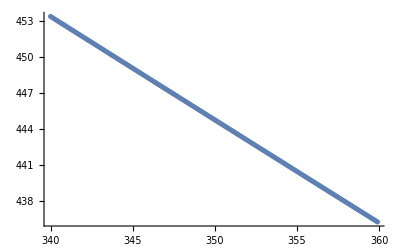

```mathematica
ListPlot[chart]
```

```mathematica
350.46317+0.46775*10
```

355.141

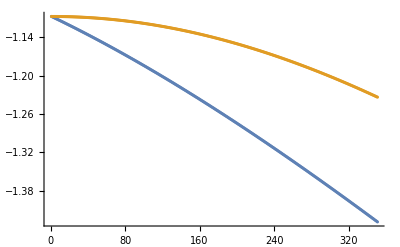

```mathematica
ListPlot[groundZeeman[[1;;2]]]
```

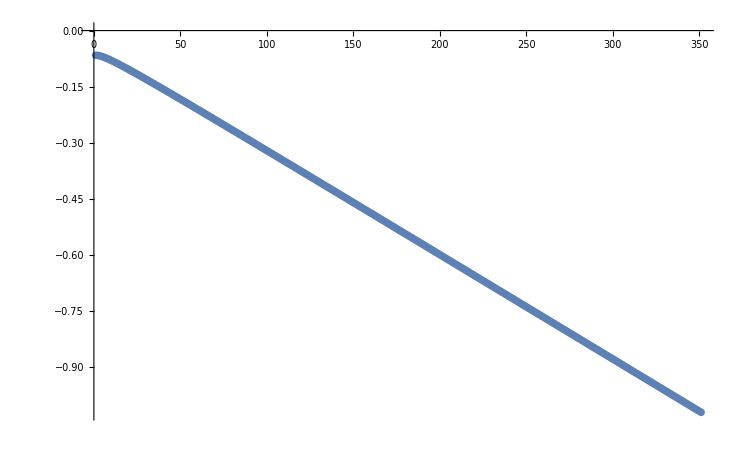

```mathematica
ListPlot[excitedZeeman[[16;;16]]]
```

```mathematica
states.(DipoleOriginal[[1,3]]/ΩR).Transpose[states]//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.128687 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000293286 | 0. | 0. | 0. | -0.22307 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00047993 | 0. | 0. | 0. | 0.315721 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000537692 | 0. | 0. | 0. | 0.407921 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.203718 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.14279 | 0. | 0. | 0. | -0.249923 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.248659 | 0. | 0. | 0. | 0.250346 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.353567 | 0. | 0. | 0. | -0.204753 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.158972 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.319617 | 0. | 0. | 0. | -0.112987 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.323803 | 0. | 0. | 0. | 0.0655775 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.292915 | 0. | 0. | 0. | -0.00146607 | 0. | 0. | 0.
0. | 0.000537651 | 0. | 0. | 0. | 0. | 0. | -0.353539 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.000481888 | 0. | 0. | 0. | 0. | 0. | 0.251336 | 0. | 0. | 0. | -0.321689 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.000295705 | 0. | 0. | 0. | 0. | 0. | 0.145893 | 0. | 0. | 0. | -0.325816 | 0. | 0.284398 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.408574 | 0. | 0. | 0. | 0. | 0. | 0.203495 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.316733 | 0. | 0. | 0. | 0. | 0. | 0.249649 | 0. | 0. | 0. | -0.063524 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.224143 | 0. | 0. | 0. | 0. | 0. | -0.25007 | 0. | 0. | 0. | 0.110601 | 0. | 0.00144469 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.129513 | 0. | 0. | 0. | 0. | 0. | 0.204526 | 0. | 0. | 0. | -0.157254 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
Style[(DipoleOriginal=WignerEckart[system,{Dipole,1}]//.ReducedME[1,{Dipole,1},2]->ΩR)//MatrixForm,Small]
```

((0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √15) | 0 | 0 | 0 | 0 | 0 | -ΩR/(2 √6) | 0 | 0 | 0 | ΩR/(2 √10) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √5) | 0 | 0 | 0 | 0 | 0 | -ΩR/4 | 0 | 0 | 0 | ΩR/(4 √5) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(√10) | 0 | 0 | 0 | 0 | 0 | -ΩR/4 | 0 | 0 | 0 | ΩR/(4 √15) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(√6) | 0 | 0 | 0 | 0 | 0 | -ΩR/(2 √6) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(4 √3) | 0 | 0 | 0 | -1/4 √(5/3) ΩR | 0 | ΩR/(2 √3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/4 | 0 | 0 | 0 | -1/4 √(5/3) ΩR | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √2) | 0 | 0 | 0 | 0
-ΩR/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ΩR/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ΩR/(√10) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ΩR/(2 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ΩR/(2 √15) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ΩR/(2 √6) | 0 | 0 | 0 | -ΩR/(2 √2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ΩR/4 | 0 | 0 | 0 | -ΩR/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ΩR/4 | 0 | 0 | 0 | -ΩR/(4 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ΩR/(2 √6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ΩR/(4 √15) | 0 | 0 | 0 | -1/4 √(5/3) ΩR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ΩR/(4 √5) | 0 | 0 | 0 | -1/4 √(5/3) ΩR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ΩR/(2 √10) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√(2/15) ΩR | 0 | 0 | 0 | 0 | 0 | ΩR/(4 √3) | 0 | 0 | 0 | ΩR/(4 √5) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 √(3/5) ΩR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √15) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√(2/15) ΩR | 0 | 0 | 0 | 0 | 0 | -ΩR/(4 √3) | 0 | 0 | 0 | ΩR/(4 √5) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | -ΩR/(2 √3) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ΩR/4 | 0 | 0 | 0 | 1/4 √(5/3) ΩR | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ΩR/4 | 0 | 0 | 0 | -1/4 √(5/3) ΩR | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -√(2/15) ΩR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 √(3/5) ΩR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -√(2/15) ΩR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ΩR/(4 √3) | 0 | 0 | 0 | -ΩR/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ΩR/(4 √3) | 0 | 0 | 0 | -ΩR/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ΩR/(4 √5) | 0 | 0 | 0 | 1/4 √(5/3) ΩR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ΩR/(2 √15) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ΩR/(4 √5) | 0 | 0 | 0 | -1/4 √(5/3) ΩR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(√6) | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(√10) | 0 | 0 | 0 | 0 | 0 | ΩR/4 | 0 | 0 | 0 | ΩR/(4 √15) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √5) | 0 | 0 | 0 | 0 | 0 | ΩR/4 | 0 | 0 | 0 | ΩR/(4 √5) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √15) | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √6) | 0 | 0 | 0 | ΩR/(2 √10) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/4 | 0 | 0 | 0 | 1/4 √(5/3) ΩR | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(4 √3) | 0 | 0 | 0 | 1/4 √(5/3) ΩR | 0 | ΩR/(2 √3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ΩR/(2 √15) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ΩR/(2 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ΩR/(√10) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ΩR/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ΩR/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ΩR/(2 √6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ΩR/4 | 0 | 0 | 0 | -ΩR/(4 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ΩR/4 | 0 | 0 | 0 | -ΩR/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ΩR/(2 √6) | 0 | 0 | 0 | -ΩR/(2 √2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ΩR/(2 √10) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ΩR/(4 √5) | 0 | 0 | 0 | 1/4 √(5/3) ΩR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ΩR/(4 √15) | 0 | 0 | 0 | 1/4 √(5/3) ΩR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0))